Intersection of Sphere with “Evaders Trace”
-In the situation where an evader moves at some distance R in a seeker’s visual field, this visualization shows the area “traced” out by the evader (green) mapped onto the sphere of radius R (transparent) overlaid the seeker’s visual field (blue).

```mathematica
α=3 π/16;(*randomly selected for visualization*)
β=π/18;(*randomly selected for visualization*)
θk=ArcTan[Tan[α/2]Cot[β/2]];
Show[ContourPlot3D[{z==Cot[α/2]x,z==Cot[β/2]y,z==-Cot[α/2]x,z==-Cot[β/2]y,x^2+y^2+z^2==1,z^2==(x/Tan[65 π/180])^2+(y/Tan[135/2 π/180])^2},{x,-1,1},{y,-1,1},{z,0,1},BoxRatios->{1, 1, 1/2},AxesLabel->{x,y,z},ContourStyle->{{Blue,Opacity[.25]},{Orange,Opacity[.25]},{Blue,Opacity[.25]},{Orange,Opacity[.25]},{Sapphire,Opacity[.25]},{Gray,Opacity[.25]}}],ContourPlot3D[x^2+y^2+z^2==1.01^2,{x,-1,1},{y,-1,1},{z,0,1.01},RegionBoundaryStyle->None,RegionFunction->Function[{x,y}, x^2+(x^2+y^2)Tan[α/2]^2<=Tan[α/2]^2&&y^2+(x^2+y^2)Tan[β/2]^2<=Tan[β/2]^2],ContourStyle->Green],
ContourPlot3D[x^2+y^2+z^2==1.001^2,{x,-1,1},{y,-1,1},{z,0,1.01},RegionBoundaryStyle->None,RegionFunction->Function[{x,y}, Tan[135/2 π/180]^2 x^2+Tan[65 π/180]^2 y^2+(x^2+y^2)Tan[65 π/180]^2 Tan[135/2 π/180]^2<=Tan[65 π/180]^2 Tan[135/2 π/180]^2],ContourStyle->101],ParametricPlot3D[{{Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2))Cos[θ],Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2))Sin[θ],√(1-Tan[α/2]^2/(Cos[θ]^2+Tan[α/2]^2))},{Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2))Cos[θ],Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2))Sin[θ],0},
{Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2))Cos[θ],Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2))Sin[θ],√(1-Tan[β/2]^2/(Sin[θ]^2+Tan[β/2]^2))},{Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2))Cos[θ],Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2))Sin[θ],0}},{θ,0,2π},PlotStyle->Red]]
```

-Graphics3D-

Projection of Evader’s Trace on to the Polar Plane
-Necessary for understanding how to find the area of the evaders trace

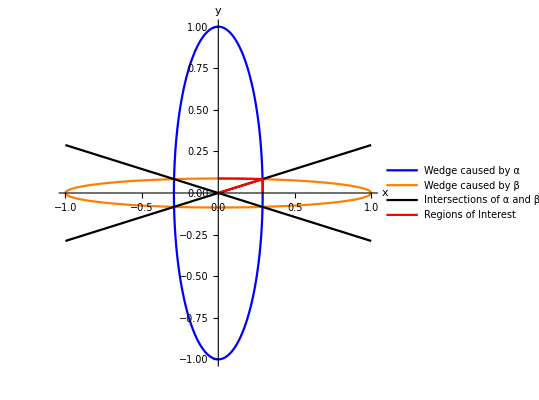

```mathematica
Legended[Show[PolarPlot[{Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2)),Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2))},{θ,0,2π},PlotRange->{-1,1},AxesLabel->{x,y},PlotStyle->{Blue,Orange}],Plot[{Cot[α/2]Tan[β/2]x,-Cot[α/2]Tan[β/2]x},{x,-1,1},PlotStyle->Black],PolarPlot[Tan[α/2]/(√(Cos[θ]^2+Tan[α/2]^2)),{θ,0,ArcTan[Cot[α/2]Tan[β/2]]},PlotStyle->Red],PolarPlot[Tan[β/2]/(√(Sin[θ]^2+Tan[β/2]^2)),{θ,ArcTan[Cot[α/2]Tan[β/2]],π/2},PlotStyle->Red],Plot[Cot[α/2]Tan[β/2]x,{x,0,Tan[α/2]/(√(Tan[β/2]^2/Tan[α/2]^2+Sec[α/2]^2))},PlotStyle->Red]],LineLegend[{Blue,Orange,Black,Red},{"Wedge caused by α","Wedge caused by β","Intersections of α and β","Regions of Interest"}]]
```

These are the two methods from the internet that break down for large angles and I believe are measuring their angles slightly differently.

```mathematica
α=2 π/16;
β=π/18;
4 R^2(ArcTan[Sin[β/2]Tan[ArcCos[(Cos[α]-Sin[β/2]^2)/Cos[β/2]^2]/2]])//N
4 R^2(ArcSin[Tan[β/2]Tan[α/2]])//N
```

0.0696138 R^2

0.0696138 R^2

Our Closed for solution for surface area of “evader trace”

```mathematica
α=2 π/16;
β=π/18;
R^2(2π-4ArcSin[(Cos[α/2]Tan[β/2])/(√(Tan[α/2]^2+Tan[β/2]^2))]-4ArcSin[(Cos[β/2]Tan[α/2])/(√(Tan[α/2]^2+Tan[β/2]^2))])//N
```

0.0680162 R^2

Plot of entire visual Field (Intersection of sphere with “Visual Cone”)

```mathematica
Show[ContourPlot3D[{x^2+y^2+z^2==1,z^2==(x/Tan[65 π/180])^2+(y/Tan[135/2 π/180])^2},{x,-1,1},{y,-1,1},{z,0,1},BoxRatios->{1,1,1/2}],ParametricPlot3D[{{(Tan[135/2 π/180]Tan[65 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2))Cos[θ],(Tan[135/2 π/180]Tan[65 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2))Sin[θ],√(1-((Tan[135/2 π/180]Tan[65 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2)))^2)},{(Tan[135/2 π/180]Tan[65 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2))Cos[θ],(Tan[135/2 π/180]Tan[65 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2))Sin[θ],0}},{θ,0,2π},PlotStyle->Red]]
```

-Graphics3D-

Projection on to polar plane

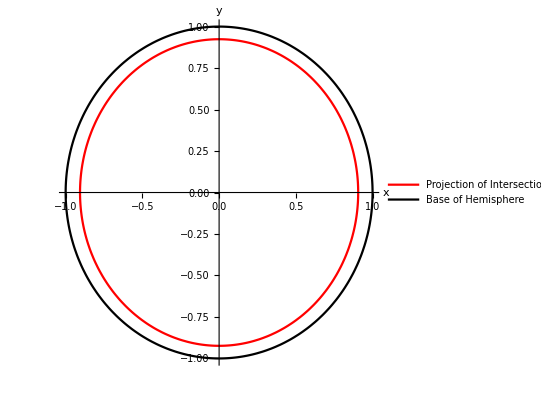

```mathematica
PolarPlot[{(Tan[65 π/180]Tan[135/2 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2)),1},{θ,0,2π},PlotStyle->{Red,Black},AxesLabel->{x,y},PlotLegends->{"Projection of Intersection","Base of Hemisphere"}]
```

Closed form Solutions for Circular cones (instead of elliptical cone). Two different cones with the different visual angles.

```mathematica
2π R^2-2π R^2 Cos[135/2 π/180]//N
2π R^2-2π R^2 Cos[65 π/180]//N
```

3.87871 R^2

3.6278 R^2

Average of the two above surface areas

```mathematica
2π R^2-π R^2 Cos[135/2 π/180]-π R^2 Cos[65 π/180]//N
```

3.75326 R^2

“Confirmation” through brute force integration

```mathematica
R^2 NIntegrate[1-√(1-((Tan[65 π/180]Tan[135/2 π/180])/(√(Tan[135/2 π/180]^2 Cos[θ]^2+Tan[65 π/180]^2 Sin[θ]^2+Tan[65 π/180]^2 Tan[135/2 π/180]^2)))^2),{θ,0,2π}]//N
```

3.7505 R^2

Transforming the evaders trace ratio into an expected probability of detection function

```mathematica
Manipulate[Plot[(b+1)x/(b x+1),{x,0,1},PlotRange->{0,1}],{b,100,2000}]
```

```mathematica
f[b_,x_]:=(b+1)x/(b x+1);
bstar=Values[Solve[f[b,.001]==.5,b]][[1,1]];(*fitting the probability of detecting a fly which takes up ~.1% of the visual field to be 50% *)
f[bstar,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(999. x)/(998. x+1)